任务1：阻尼振动的完整分析

```mathematica
(*清除变量*)Clear["Global`*"]

(*定义微分方程左边*)
eqn=m*x''[t]+gamma*x'[t]+k*x[t]==0;

(*1. 求通解*)
generalSol=DSolve[eqn,x[t],t];
Print["通解 x(t) = ",generalSol[[1,1,2]]]

(*2. 定义参数和初始条件*)
mVal=1;kVal=1;
initConds={x[0]==1,x'[0]==0};

(*定义求解特定 gamma 的函数*)
solveForGamma[g_]:=Module[{sol},sol=DSolveValue[{eqn/. {m->mVal,k->kVal,gamma->g},initConds},x[t],t];
Simplify[sol] (*化简结果*)];

(*求解三种情况*)
solUnder=solveForGamma[0.2];(*欠阻尼*)solCrit=solveForGamma[2];(*临界阻尼*)solOver=solveForGamma[4];(*过阻尼*)Print["欠阻尼 (gamma=0.2): x(t) = ",solUnder]
Print["临界阻尼 (gamma=2): x(t) = ",solCrit]
Print["过阻尼 (gamma=4): x(t) = ",solOver]
```

通解 x(t) = ⅇ^(1/2 (-gamma/m-(√(gamma^2-4 k m))/m) t) C[1]+ⅇ^(1/2 (-gamma/m+(√(gamma^2-4 k m))/m) t) C[2]

欠阻尼 (gamma=0.2): x(t) = ⅇ^(-0.1 t) (1. Cos[0.994987 t]+0.100504 Sin[0.994987 t])

临界阻尼 (gamma=2): x(t) = ⅇ^-t (1+t)

过阻尼 (gamma=4): x(t) = 1/6 ⅇ^(-((2+√3) t)) (3-2 √3+(3+2 √3) ⅇ^(2 √3 t))

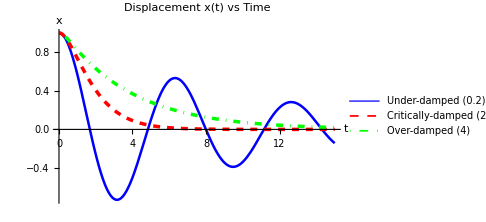
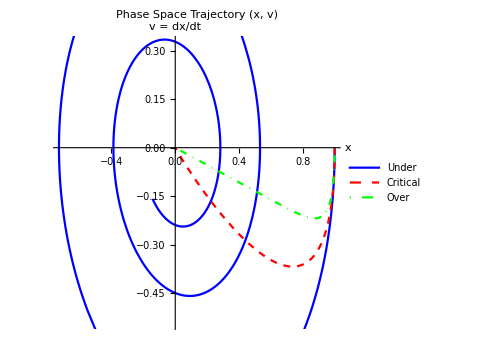
-Graphics- | -Graphics-

```mathematica
(*1. x(t) 曲线比较*)plotXt=Plot[{solUnder,solCrit,solOver},{t,0,15},PlotStyle->{{Blue,Thickness[0.005]},{Red,Dashed,Thickness[0.007]},{Green,DotDashed,Thickness[0.007]}},PlotLegends->{"Under-damped (0.2)","Critically-damped (2)","Over-damped (4)"},PlotLabel->"Displacement x(t) vs Time",AxesLabel->{"t","x"},ImageSize->Medium];

(*2. 相空间轨迹 (x,v)*)
(*计算速度 v(t)=x'(t)*)
vUnder=D[solUnder,t];
vCrit=D[solCrit,t];
vOver=D[solOver,t];

plotPhase=ParametricPlot[{{solUnder,vUnder},{solCrit,vCrit},{solOver,vOver}},{t,0,15},PlotStyle->{Blue,{Red,Dashed},{Green,DotDashed}},PlotLegends->{"Under","Critical","Over"},PlotLabel->"Phase Space Trajectory (x, v)",AxesLabel->{"x","v = dx/dt"},AspectRatio->1,ImageSize->Medium];

(*显示两张图*)
Grid[{{plotXt,plotPhase}}]
```

任务2：简单受迫振动

共振频率 omega_res = 0.989949

最大振幅 A_max = 5.02519

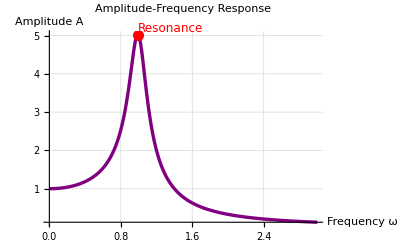

```mathematica
(*定义参数*)mVal=1;kVal=1;gammaVal=0.2;F0=1;

(*方法：假设稳态解形式为 X*Exp[I omega t]，代入方程求解复振幅 X*)
(*对应的代数方程：(-m w^2+I gamma w+k) X=F0*)
(*振幅 A=Abs[X]*)

ampFunc[w_]:=Abs[F0/(-mVal*w^2+I*gammaVal*w+kVal)];

(*1. 寻找共振频率和最大振幅*)
(*Maximize 可能会尝试符号求解，FindMaximum 更适合数值*)
maxRes=FindMaximum[ampFunc[w],{w,0.8}];(*在 1 附近寻找*)resFreq=w/. maxRes[[2]];
maxAmp=maxRes[[1]];

Print["共振频率 omega_res = ",resFreq]
Print["最大振幅 A_max = ",maxAmp]

(*2. 绘制幅频响应曲线*)
Plot[ampFunc[w],{w,0,3},PlotRange->All,PlotStyle->{Purple,Thickness[0.006]},Epilog->{Red,PointSize[0.02],Point[{resFreq,maxAmp}],Text[Style["Resonance",12,Red],{resFreq,maxAmp},{-1.2,-1}]},PlotLabel->"Amplitude-Frequency Response",AxesLabel->{"Frequency ω","Amplitude A"},GridLines->Automatic]
```

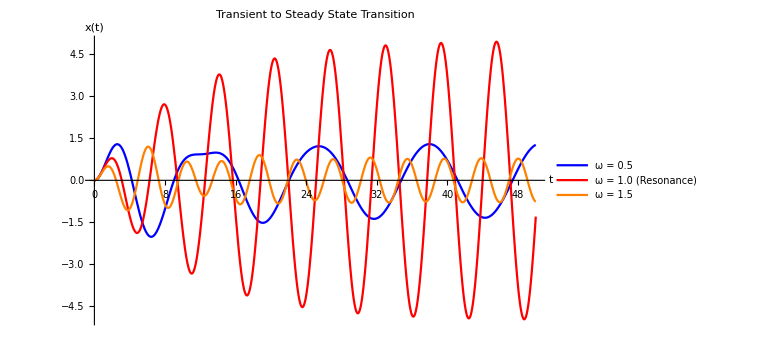

```mathematica
(*定义受迫振动方程*)forcedEq[w_]:={mVal*x''[t]+gammaVal*x'[t]+kVal*x[t]==F0*Cos[w*t],x[0]==0,x'[0]==0};

(*分别求解三个频率*)
omegas={0.5,1.0,1.5};
sols=Table[NDSolveValue[forcedEq[w],x[t],{t,0,50}],{w,omegas}];

(*绘图比较*)
Plot[sols,{t,0,50},PlotLegends->{"ω = 0.5","ω = 1.0 (Resonance)","ω = 1.5"},PlotStyle->{Blue,Red,Orange},PlotLabel->"Transient to Steady State Transition",AxesLabel->{"t","x(t)"},ImageSize->Large]
```